## Define Hamiltonian and useful functions

```mathematica
Clear[findEvolutionOperator4D, funcs, ψ0, equations, Uuncut]
findEvolutionOperator4D[HamIn_, Tmax_, acc_:10]:=(
isToKeep = {1, 2, 3, 5, 6};
statesToKeep = Table[8*i + j - 8, {i, isToKeep}, {j, isToKeep}] // Flatten;
Ham = HamIn[[statesToKeep, statesToKeep]];

funcs=Array[ψ[#2 + 4*(#1- 1)][t]&,{Length[statesToKeep], 4}];
ψ0 = Table[0, {i, Length[statesToKeep]}, {j, 4}];
ψ0[[1, 1]] = 1.;
ψ0[[2, 2]] = 1.;
ψ0[[1 + Length[isToKeep], 3]] = 1.;
ψ0[[2 + Length[isToKeep], 4]] = 1.;


equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==ψ0/.t->0]];
Uuncut = NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->acc, PrecisionGoal->acc, EvaluationMonitor:>showStatus["Tmax = "<>ToString[AccountingForm[Tmax]]<>"          t = "<>ToString[CForm[t]]]];
Uuncut[[{1, 2, 1 + Length[isToKeep], 2 + Length[isToKeep]}]]
)

ClearAll[debug];
SetAttributes[debug,HoldAll];
debug[code_]:=Internal`InheritedBlock[{Message},Module[{inMessage},Unprotect[Message];
Message[args___]/;!MatchQ[First[Hold[args]],_$Off]:=Block[{inMessage=True},Print[{Shallow/@Replace[#,HoldForm[f_[___]]:>HoldForm[f],1],Style[Map[Short,Last[#],{2}],Red]}&@Drop[Drop[Stack[_],-7],4]];
Message[args];
Throw[$Failed,Message];]/;!TrueQ[inMessage];
Protect[Message];];
Catch[StackComplete[code],Message]]

CZangle[M_] := (
z = (M[[4, 4]]*M[[1, 1]])/(M[[2, 2]]*M[[3, 3]]);
ArcTan[Re[z], Im[z]]
)
Zangle[M_] := (
z = M[[2, 2]]/M[[1, 1]];
ArcTan[Re[z], Im[z]]
)
```

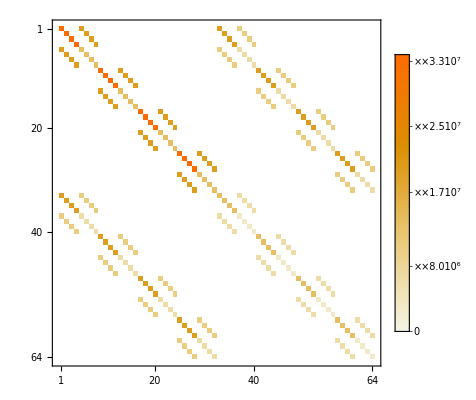

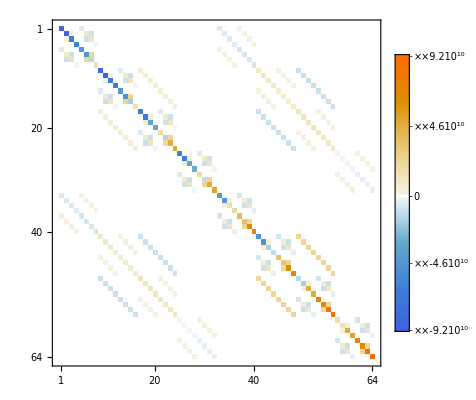

```mathematica
Vdip = (d*e)^2/(4*π*8.85418782×10^-12*11.7*dDip^3*h/(2π));
Hdip = Vdip*TProduct[TProduct[ii, σI, σI], TProduct[ii, σI, σI]];

H2 = TProduct[Hexact, IdentityMatrix[8]] + TProduct[IdentityMatrix[8], Hexact] + Hdip;

setVariables[]

ΔE = 2000;

MatrixPlot[Hdip, PlotLegends->True]

Bamp[t_] := 0
Eamp[t_] := 0
MatrixPlot[H2, PlotLegends->True]

clearVariables[]
```

## Look at single qubit evolution

```mathematica
setVariables[]

Tmax = 10^-6;

ΔE = 2000;

Eamp[t_] := 30*cosWindow[t, Tmax/3, Tmax];
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2) - 2*π*20*10^6;

(* turn off oscillatin' magnetic field *)
Bamp[t_] := 0
ωB = (ωB + ωE)/2;

statesInOrder[Hcorrected /. t->Tmax/2] // MatrixForm

Hcorrected[[1, 5]]

Vdip*((statesInOrder[Hcorrected /. t->Tmax/2][[2, 2]])^2 - (statesInOrder[Hcorrected /. t->Tmax/2][[1, 1]])^2)^2 / (2*π)

(*U = findEvolutionOperator2D[Hcorrected, Tmax];

(*Abs[Uax[[1]][[5]]]^2 /. t->Tmax/2
Abs[Uax[[2]][[6]]]^2 /. t->Tmax/2*)

Evaluate@Table[Max[Abs[Uuncut[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[Uuncut[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]*)


clearVariables[]
```

setVariables[]

Part::partd: Part specification dState⟦1⟧ is longer than depth of object.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -40000000 π+ωB+2 π (-A/4+ϵ0+A dState⟦1⟧^2).

statesInOrder[Hcorrected]

Part::partd: Part specification Hcorrected⟦1,5⟧ is longer than depth of object.

Hcorrected⟦1,5⟧

Part::partw: Part 2 of statesInOrder[Hcorrected] does not exist.

Part::partd: Part specification statesInOrder[Hcorrected]⟦1,1⟧ is longer than depth of object.

(7.68167×10^8 d^2 e^2 (-(statesInOrder[Hcorrected]⟦1,1⟧)^2+(statesInOrder[Hcorrected]⟦2,2⟧)^2)^2)/(dDip^3 h)

clearVariables[]

## Estimate theoretical transition rate

```mathematica
setVariables[]

ΔE = 2000;
Ea = 40;
Eamp[t_] := Ea
ωE = 2*π*(ϵ0 + A/4 - A*dState[[1]]^2/2) + 2*π*5*10^6;
Bamp[t_] := 0

(statesInOrder[Hcorrected] // Transpose) // MatrixForm
Λge.(statesInOrder[Hcorrected] // Transpose) // MatrixForm
(1/(2π))*Vdip*(((Λge.(statesInOrder[Hcorrected] // Transpose))[[2, 2]])^2 - ((Λge.(statesInOrder[Hcorrected] // Transpose))[[1, 1]])^2)^2

clearVariables[]
```

(0.711042 | 1.10441×10^-18 | 2.95784×10^-17 | 0. | 0.70315 | -4.32029×10^-19 | -1.72787×10^-18 | 0.
5.65318×10^-18 | -0.929595 | -0.0000359802 | 0. | 1.04665×10^-16 | 0.368581 | -0.0000122188 | 0.
6.30989×10^-17 | -0.00182929 | -0.942895 | 0. | 1.12978×10^-16 | -0.00471671 | -0.333051 | 0.
0. | 0. | 0. | 0.776899 | 0. | 0. | 0. | 0.629626
-0.70315 | 3.85976×10^-17 | -2.22045×10^-16 | 0. | 0.711042 | -3.1225×10^-17 | -1.66533×10^-16 | 0.
-2.4142×10^-19 | 0.368577 | -0.00478268 | 0. | 5.66312×10^-19 | 0.929584 | -0.00164911 | 0.
0. | 0.0000135547 | 0.333055 | 0. | -2.65532×10^-17 | 0.0000354402 | -0.942907 | 0.
0. | 0. | 0. | -0.629626 | 0. | 0. | 0. | 0.776899)

(0.899918 | -1.1411×10^-17 | 9.96544×10^-17 | 0. | 0.436058 | 9.66808×10^-18 | 5.21085×10^-17 | 0.
5.42861×10^-18 | -0.998804 | 0.00150942 | 0. | 9.88823×10^-17 | 0.0488634 | 0.000520638 | 0.
5.97228×10^-17 | -0.00173578 | -0.999929 | 0. | 1.15502×10^-16 | -0.00447577 | -0.0109345 | 0.
0. | 0. | 0. | 0.938524 | 0. | 0. | 0. | 0.345215
-0.436058 | 3.68888×10^-17 | -2.00618×10^-16 | 0. | 0.899918 | -2.96937×10^-17 | -1.58181×10^-16 | 0.
1.5959×10^-18 | 0.0488553 | -0.00453839 | 0. | 3.43137×10^-17 | 0.998794 | -0.00156482 | 0.
2.03634×10^-17 | -0.000577521 | 0.0109423 | 0. | 1.13279×10^-17 | -0.00148864 | -0.999939 | 0.
0. | 0. | 0. | -0.345215 | 0. | 0. | 0. | 0.938524)

1.88836×10^6

## Optimize a CZ gate

```mathematica
angle[z_] := ArcTan[Re[z], Im[z]]
CZangle[M_] := (
z = (M[[4, 4]]*M[[1, 1]])/(M[[2, 2]]*M[[3, 3]]);
ArcTan[Re[z], Im[z]]
)
fidelityToCZWithLocalZs[M_] := (
angles = Table[ArcTan[Re[u], Im[u]], {u, Diagonal[M]}];

U2afterGates = U2*E^(-ⅈ*angles[[1]]) /. t->Tmax;

pZ = {{1, 0}, {0, E^(-ⅈ*(angles[[2]] - angles[[1]]))}};
U2afterGates = TProduct[pZ, pZ].U2afterGates;

CZ = DiagonalMatrix[{1, 1, 1, -1}];

fidelity[ConjugateTranspose[CZ].U2afterGates]
)

Clear[fidelityCZ];
fidelityCZ[EaIn_?NumericQ, acc_:10] := (
Clear[Eamp];
Eamp[t_] := EaIn*tanhWindow[t,Tmax/5,Tmax]^2 ;

Ubase = MatrixExp[-ⅈ*t*DiagonalMatrix[energiesInOrder[HcorrectedStatic]]];

U2 = (ConjugateTranspose[TProduct[Ubase, Ubase]])[[{1, 2, 9, 10}, {1, 2, 9, 10}]].findEvolutionOperator4D[H2, acc];

F = fidelityToCZWithLocalZs[U2 /. t->Tmax];

Print[{F, CZangle[U2 /. t->Tmax], {ΔE, B0, EaIn, 0, ωE, ωB, Tmax}}];

F
)
```

```mathematica
setVariables[]

ΔE = -3000;

Tmax = 1000*10^-9;

(* set Eac *)
ωE = 2*π*(ϵ0 + A/4 - (A*dState[[1]]^2/2)) - 2*π*1.7*10^7;
(*Eamp[t_] := 20*tanhWindow[t,Tmax/5, Tmax]^2 ;*)

(* turn off oscillatin' magnetic field *)
ωB = (ωB + ωE)/2;
Bamp[t_] := 0

Clear[map]
map[x_, a_, b_] := a + (b - a)*x // Re

TimeConstrained[(
bestSoFar = 0;
bestParameters = {};

NMaximize[
{
fidelityCZ[
map[x1, 10, 60]
],
0 < x1 < 1
},
{{x1, .3, .7}},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]

), 60*60*10
]

clearVariables[]
```

### Generate a Spectrum of C-phase Gates

```mathematica
CphaseParameters[T_] := (
setVariables[];

Tmax = T;

T1 = 5*10^-9;
T2 = Tmax - 2*T1;
T3 = Min[T2/2, 300*10^-9];

Clear[ΔE];

Ea = 40*Min[1, (T3/(300*10^-9))^2];
Eamp[t_] := Ea*cosWindow[t - T1, T3, T2];
ωE = 2*π*(ϵ0 + A/4 - A*dState[[1]]^2/2) - 2*π*10*10^6 /. ΔE->2000;

Bamp[t_] := 0;
ωB = (ωB + ωE)/2;

ΔE = 10000 - 8000*twoPointWindow[t, T1, Tmax, 1];

Ubase = MatrixExp[-ⅈ*t*(H2[[{1, 2, 9, 10}, {1, 2, 9, 10}]] /. t->0)];

U = findEvolutionOperator4D[H2, Tmax];

Ufinal = ConjugateTranspose[Ubase].U /. t->Tmax;
ϕ = CZangle[Ufinal];
ϕz = -Zangle[Ufinal];

pNonAd = 1 - Sum[Abs[Ufinal[[i, i]]]^2, {i, 4}]/4;

Print[{Tmax, ϕ, ϕz, pNonAd}];
clearVariables[];

{ϕ, ϕz, pNonAd}

)

CphaseParams = {};
Do[AppendTo[CphaseParams, Join[{T}, CphaseParameters[T]]], {T, 0, 1000*10^-9, 50*10^-9}];
CphaseParams
```

{0,0.,0.,0.}

{1/20000000,-9.23297×10^-6,-1.53255,0.0000577732}

{1/10000000,-0.00120546,2.92285,0.0000775931}

{3/20000000,-0.00697096,1.07783,0.0000930515}

{1/5000000,-0.0308948,-0.82825,0.0000744578}

{1/4000000,-0.107289,-2.88782,-0.0000114645}

{3/10000000,-0.306611,1.02244,0.000160276}

{7/20000000,-0.717414,-1.86741,0.000131107}

{1/2500000,-1.38535,0.838639,0.0000621861}

{9/20000000,-2.2691,2.78622,0.000501338}

{1/2000000,3.01769,-2.28524,0.000112301}

{11/20000000,2.0198,-1.73561,0.000462147}

{3/5000000,1.10597,-1.75569,0.0000380805}

{13/20000000,0.326179,-0.896936,0.0000313311}

{7/10000000,-0.440949,0.254573,0.0000478122}

{3/4000000,-1.20799,1.40619,-0.0000153779}

{1/1250000,-1.97515,2.55767,5.80604×10^-6}

{17/20000000,-2.74217,-2.57388,-0.0000440581}

{9/10000000,2.77382,-1.42242,-0.0000264573}

{19/20000000,2.00683,-0.27077,-0.0000549046}

{1/1000000,1.23961,0.880673,-0.0000465595}

{{0,0.,0.,0.},{1/20000000,-9.23297×10^-6,-1.53255,0.0000577732},{1/10000000,-0.00120546,2.92285,0.0000775931},{3/20000000,-0.00697096,1.07783,0.0000930515},{1/5000000,-0.0308948,-0.82825,0.0000744578},{1/4000000,-0.107289,-2.88782,-0.0000114645},{3/10000000,-0.306611,1.02244,0.000160276},{7/20000000,-0.717414,-1.86741,0.000131107},{1/2500000,-1.38535,0.838639,0.0000621861},{9/20000000,-2.2691,2.78622,0.000501338},{1/2000000,3.01769,-2.28524,0.000112301},{11/20000000,2.0198,-1.73561,0.000462147},{3/5000000,1.10597,-1.75569,0.0000380805},{13/20000000,0.326179,-0.896936,0.0000313311},{7/10000000,-0.440949,0.254573,0.0000478122},{3/4000000,-1.20799,1.40619,-0.0000153779},{1/1250000,-1.97515,2.55767,5.80604×10^-6},{17/20000000,-2.74217,-2.57388,-0.0000440581},{9/10000000,2.77382,-1.42242,-0.0000264573},{19/20000000,2.00683,-0.27077,-0.0000549046},{1/1000000,1.23961,0.880673,-0.0000465595}}

```mathematica
unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)
Do[
CphaseParams[[All, i]] = unravel[CphaseParams[[All, i]]],
{i, {2, 4}}];

ϕFn = Interpolation[CphaseParams[[All, {1, 2}]]];


Figure[{
FigurePanel[{
FigGraphics[
Plot[ϕFn[T*10^-9], {T, 0, 1000}, PlotStyle->Blue]
]
},
XPlotRange->{0, 700}, XFrameLabel->"T (ns)",
YPlotRange->{-2π - .5, 0 + .3}, YFrameLabel->"ϕ", YTicks->LinTicksPi[-3π, π, π/2, 4, {"-3π", "-5π/2", "-2π", "-3π/2", "-π", "-π/2", "0", "π/2", "π"}]
];
},CanvasSize->{5,2}]

Export["CZgateAngles.eps", %]
```

-Graphics-

CZgateAngles.eps

```mathematica
NMinimize[Abs[ϕFn[ttt] + π], ttt]
```

InterpolatingFunction::dmval: Input value {-0.829053} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.969346} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.912378} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.000381433,{ttt→4.9388×10^-7}}

```mathematica
Hrot - (Hrot /. Δγ->0) // Apart // MatrixForm
```

(-1/2 B0 π γe Δγ+(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (B0 ⅇ^(-ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
0 | -1/2 B0 π γe Δγ+(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | (B0 ⅇ^(-ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
0 | 0 | 1/2 B0 π γe Δγ-(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(B0 ⅇ^(-ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
0 | 0 | 0 | 1/2 B0 π γe Δγ-(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -(B0 ⅇ^(-ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2))
(B0 ⅇ^(ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -1/2 B0 π γe Δγ-(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0
0 | (B0 ⅇ^(ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | -1/2 B0 π γe Δγ-(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0
0 | 0 | -(B0 ⅇ^(ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | 1/2 B0 π γe Δγ+(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0
0 | 0 | 0 | -(B0 ⅇ^(ⅈ t ωE) h π Vt γe Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)) | 0 | 0 | 0 | 1/2 B0 π γe Δγ+(B0 d e π γe ΔE Δγ)/(2 √(h^2 Vt^2+d^2 e^2 ΔE^2)))